```mathematica
A={{1,0,0,0,0},{16,-32,16,0,0},{0,16,-32,16,0},{0,0,16,-32,16},{0,0,0,0,1}}
```

{{1,0,0,0,0},{16,-32,16,0,0},{0,16,-32,16,0},{0,0,16,-32,16},{0,0,0,0,1}}

```mathematica
B=Inverse[A];
B//MatrixForm
```

(1 | 0 | 0 | 0 | 0
3/4 | -3/64 | -1/32 | -1/64 | 1/4
1/2 | -1/32 | -1/16 | -1/32 | 1/2
1/4 | -1/64 | -1/32 | -3/64 | 3/4
0 | 0 | 0 | 0 | 1)

```mathematica
B.{0,1/4,1/2,3/4,0}
```

{0,-5/128,-1/16,-7/128,0}

```mathematica
X=Table[{(j-1)/4,(B.DiagonalMatrix[{1,4,4,4,1}])[[j,i]]},{i,1,5},{j,1,5}];
X2=Table[{(j-1)/4,(B.DiagonalMatrix[{0,1/4,1/2,3/4,0}])[[j,i]]},{i,1,5},{j,1,5}];
```

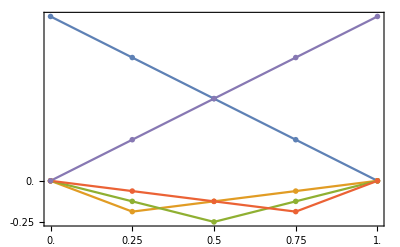

```mathematica
g1=ListPlot[X,Joined->True,Frame->True,FrameTicks->N@{{{0,-1/4},None},{{0,1/4,1/2,3/4,1},None}},PlotMarkers->•,ImagePadding->{{50,50},{20,20}}]
```

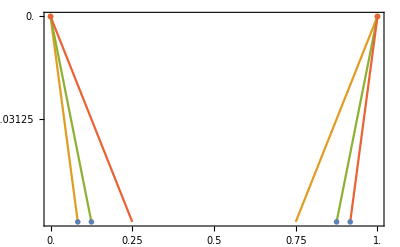

```mathematica
g2=ListPlot[X,Joined->True,Frame->True,FrameTicks->N@{{{0,-1/32},None},{{0,1/4,1/2,3/4,1},None}},PlotMarkers->•,PlotRange->{{0,1},{-1/16,0}},ImagePadding->{{70,10},{20,20}}]
```

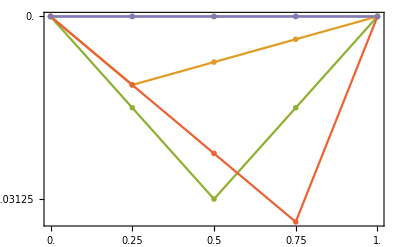

```mathematica
g3=ListPlot[X2,Joined->True,Frame->True,FrameTicks->N@{{{-1/32,0,1},None},{{0,1/4,1/2,3/4,1},None}},PlotMarkers->•,ImagePadding->{{70,10},{20,20}}]
```

```mathematica
Export[NotebookDirectory[]<>"img/g1.pdf",g1];
Export[NotebookDirectory[]<>"img/g2.pdf",g2];
Export[NotebookDirectory[]<>"img/g3.pdf",g3];
```

```mathematica
M={{-h,1,0,0,0},{h,-2,1,0,0},{0,1,-2,1,0},{0,0,1,-2,h},{0,0,0,1,-h}}
```

{{-h,1,0,0,0},{h,-2,1,0,0},{0,1,-2,1,0},{0,0,1,-2,h},{0,0,0,1,-h}}

```mathematica
NullSpace[M]
```

{{1,h,h,h,1}}

```mathematica
A={{-4,4,0,0,0},{16,-32,16,0,0},{0,16,-32,16,0},{0,0,16,-32,16},{0,0,0,0,1}};
A//MatrixForm
```

(-4 | 4 | 0 | 0 | 0
16 | -32 | 16 | 0 | 0
0 | 16 | -32 | 16 | 0
0 | 0 | 16 | -32 | 16
0 | 0 | 0 | 0 | 1)

```mathematica
B=Inverse[A]//MatrixForm
```

(-1 | -3/16 | -1/8 | -1/16 | 1
-3/4 | -3/16 | -1/8 | -1/16 | 1
-1/2 | -1/8 | -1/8 | -1/16 | 1
-1/4 | -1/16 | -1/16 | -1/16 | 1
0 | 0 | 0 | 0 | 1)

{{0,1},{0,1,2}}

```mathematica
G[x_,y_]:=Piecewise[{{x(y-1),0<x<y},{y(x-1),y<x<1}}]
```

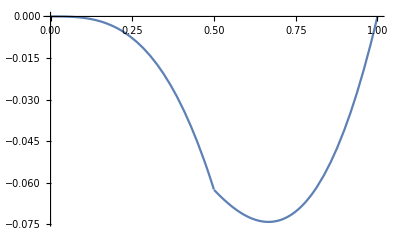

```mathematica
Plot[x^2 G[.5,x],{x,0,1}]
```